## Setup

```mathematica
R=10;
n=21;
h=R/(n-1);
(c=Table[1,{i,n}])//MatrixForm;
(r=h Table[i-1,{i,n}])//MatrixForm;
```

```mathematica
symm[i_]=If[i>=1,i,2-i];
```

```mathematica
(grad6=1/h Table[
(If[j==symm[i-3],-1,0]+
If[j==symm[i-2],+9,0]+
If[j==symm[i-1],-180/4,0]+
If[j==symm[i+1],180/4,0]+
If[j==symm[i+2],-9,0]+
If[j==symm[i+3],+1,0])/60,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad8=1/h Table[
(     If[j==symm[i-4],+1,0]+
If[j==symm[i-3],-(280*4)/105,0]+
If[j==symm[i-2],+280/5,0]+
If[j==symm[i-1],-280*4/5,0]+
If[j==symm[i+1],+280*4/5,0]+
If[j==symm[i+2],-280/5,0]+
If[j==symm[i+3],+(280*4)/105,0]+
If[j==symm[i+4],-1,0])/280,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(W=h DiagonalMatrix[Table[
If[i==1,1/2,1],
{i,n}]])//MatrixForm;
```

```mathematica
(B=DiagonalMatrix[Table[0,{i,n}]])//MatrixForm;
```

```mathematica
(div6=Inverse[W].Transpose[B-W.grad6])//MatrixForm;
(div8=Inverse[W].Transpose[B-W.grad8])//MatrixForm;
```

```mathematica
(QV=DiagonalMatrix[Table[q[i],{i,n}]])//MatrixForm;
```

### 6th Order

```mathematica
order=5;
QV6=DiagonalMatrix[Table[If[i≤1,q[i],r[[i]]^2],{i,n}]];
(QS6= QV6
+Table[Which[i≤order&&j≤order,
Which[
j>i,q[i,j],
j<i,q[j,i],
True,0],
True,0],{i,n},{j,n}]
(*+Table[If[i≤n-3&& j≤n-3,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]*)
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | 1/4 | q[2,3] | q[2,4] | q[2,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | 1 | q[3,4] | q[3,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | 9/4 | q[4,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 25/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 49/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 169/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 225/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 289/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 361/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100)

```mathematica
(cond6a=div6.QV6.r^1-3QS6.c)//MatrixForm;
(cond6b=div6.QV6.r^3-5QS6.r^2)//MatrixForm;
(cond6c=div6.QV6.r^5-7QS6.r^4)//MatrixForm;
(cond6d=div6.QV6.r^7-9QS6.r^6)//MatrixForm;
```

```mathematica
(*
cond6a[[;;5]],
cond6b[[;;4]],
cond6c[[;;2]]
*)
```

```mathematica
(cond6=Join[
cond6a[[;;5]],
cond6b[[;;4]],
cond6c[[;;2]]
])//MatrixForm;
(vars6 = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
RealQ[x_]:=!(Element[x,Reals]===True)
vars6 =Select[vars6,RealQ];
Length[vars6]
Length[cond6]
```

11

11

```mathematica
(solq6=Solve[cond6==0,vars6][[1]])//MatrixForm
```

(q[1]→117/784
q[1,2]→-227/3136
q[1,3]→-43/224
q[1,4]→3141/21952
q[1,5]→-307/10976
q[2,3]→153/784
q[2,4]→-58/343
q[2,5]→1017/21952
q[3,4]→113/5488
q[3,5]→-261/10976
q[4,5]→17/3136)

```mathematica
(QQS6 = QS6/.solq6)//MatrixForm//N;
QQV6=QV6/.solq6;
```

```mathematica
PositiveDefiniteMatrixQ[QQS6]
```

True

```mathematica
(DDIV6 = Inverse[QQS6].div6.QQV6)//N//MatrixForm;
```

```mathematica
DDIV6.r//FullSimplify//MatrixForm
```

(3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
1817/720
137681/21660
-6527/600)

```mathematica
(DDIV6.r^3-5 r^2)//FullSimplify//MatrixForm//N
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
-52.5219
364.765
-1498.31)

```mathematica
(DDIV6.r^5-7 r^4)//FullSimplify//MatrixForm//N
```

(4.21691
-1.98417
3.62261
-0.501948
0.203829
0.09
0.0625
0.0459184
0.0351563
0.0277778
0.0225
0.018595
0.015625
0.0133136
0.0114796
0.01
0.00878906
0.00778547
-5790.53
39575.9
-161470.)

```mathematica
(vals6=Eigenvalues[N[DDIV6]])//MatrixForm
```

(-4.16307+0. ⅈ
-0.00126294+3.11613 ⅈ
-0.00126294-3.11613 ⅈ
-0.00405535+2.95349 ⅈ
-0.00405535-2.95349 ⅈ
-0.00589363+2.69746 ⅈ
-0.00589363-2.69746 ⅈ
-0.00408715+2.36725 ⅈ
-0.00408715-2.36725 ⅈ
0.0028552+1.98404 ⅈ
0.0028552-1.98404 ⅈ
1.78626+0. ⅈ
0.0144099+1.56706 ⅈ
0.0144099-1.56706 ⅈ
0.0281127+1.13055 ⅈ
0.0281127-1.13055 ⅈ
0.0403698+0.682864 ⅈ
0.0403698-0.682864 ⅈ
0.0476417+0.228456 ⅈ
0.0476417-0.228456 ⅈ
0.+0. ⅈ)

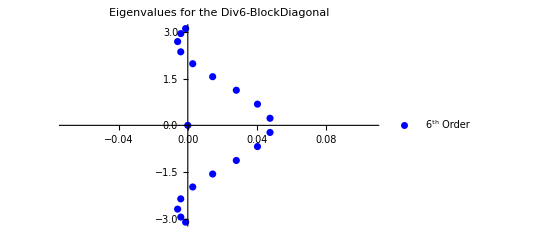

```mathematica
cplot6=ComplexListPlot[vals6,PlotRange->Automatic, AspectRatio->1/GoldenRatio,PlotStyle->Blue,PlotLegends->{"6^th Order"},PlotLabel->"Eigenvalues for the Div6-BlockDiagonal"]
```

```mathematica
order=6;
QV8=DiagonalMatrix[Table[If[i≤1,q[i],r[[i]]^2],{i,n}]];
(QS8= QV8
+Table[Which[i≤order&&j≤order,
Which[
j>i,q[i,j],
j<i,q[j,i],
True,0],
True,0],{i,n},{j,n}]
(*+Table[If[i≤n-3&& j≤n-3,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]*)
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | q[1,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | 1/4 | q[2,3] | q[2,4] | q[2,5] | q[2,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | 1 | q[3,4] | q[3,5] | q[3,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | 9/4 | q[4,5] | q[4,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | 4 | q[5,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,6] | q[2,6] | q[3,6] | q[4,6] | q[5,6] | 25/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 49/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 169/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 225/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 289/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 361/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100)

```mathematica
(*QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], 1, q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], 4, q[3,4], q[3,5], q[3,6], q[3,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], 9, q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], 16, q[5,6], q[5,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], 25, q[6,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, q[3,7], q[4,7], q[5,7], q[6,7], 36, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 49, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 64, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 81, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 100, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 121, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 144, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 169, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 196, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 225, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 256, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 289, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 324, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 361, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 400}});*)
```

```mathematica
(cond8a=div8.QV8.r^1-3QS8.c)//MatrixForm;
(cond8b=div8.QV8.r^3-5QS8.r^2)//MatrixForm;
(cond8c=div8.QV8.r^5-7QS8.r^4)//MatrixForm;
(cond8d=div8.QV8.r^7-9QS8.r^6)//MatrixForm;
```

```mathematica
(*
cond8a[[;;10]],
cond8b[[;;6]],
cond8c[[;;3]],
cond8d[[;;2]]
*)
```

```mathematica
(*
cond8a[[;;6]],
cond8b[[;;5]],
cond8c[[;;3]],
cond8d[[;;2]]
*)
```

```mathematica
(*cond8a[[;;7]],
cond8b[[;;6]],
cond8c[[;;5]],
cond8d[[;;2]]*)
```

```mathematica
(cond8=Join[
cond8a[[;;6]],
cond8b[[;;5]],
cond8c[[;;3]],
cond8d[[;;2]]
])//MatrixForm;
(vars8 = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
RealQ[x_]:=!(Element[x,Reals]===True)
vars8 =Select[vars8,RealQ];
Length[vars8]
Length[cond8]
```

16

16

```mathematica
(solq8=Solve[cond8==0,vars8][[1]])//MatrixForm
```

(q[1]→64/985
q[1,2]→-1897/59100
q[1,3]→-30896/310275
q[1,4]→26247/275800
q[1,5]→-29536/930825
q[1,6]→4861/1489320
q[2,3]→6479/62055
q[2,4]→-2488/20685
q[2,5]→8843/148932
q[2,6]→-10616/930825
q[3,4]→3481/173754
q[3,5]→-48784/1303155
q[3,6]→3343/265950
q[4,5]→2053/212760
q[4,6]→-29776/6515775
q[5,6]→2447/17375400)

```mathematica
(QQS8 = QS8/.solq8)//MatrixForm//N;
QQV8=QV8/.solq8;
```

```mathematica
PositiveDefiniteMatrixQ[QQS8]
```

True

```mathematica
(DDIV8= Inverse[QQS8].div8.QQV8)//MatrixForm//N;
```

```mathematica
DDIV8.r//FullSimplify//MatrixForm
```

(3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
3
36003/11560
23003/11340
2161333/303240
-337/30)

```mathematica
DDIV8.r^3-5 r^2//FullSimplify//MatrixForm
```

(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
583443/46240
-300079/2835
540521773/1212960
-321997/210)

```mathematica
DDIV8.r^5-7 r^4//FullSimplify//MatrixForm//N
```

(-0.0886967
0.0235832
-0.0136522
0.041412
-0.0373787
0.0102551
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1391.1
-11517.1
48018.5
-164895.)

```mathematica
DDIV8.r^7-9 r^6//MatrixForm//N
```

(-21.7646
3.9609
-13.0399
2.17273
-1.16374
-0.269432
-0.25
-0.183673
-0.140625
-0.111111
-0.09
-0.0743802
-0.0625
-0.0532544
-0.0459184
-0.04
-0.0351563
153369.
-1.25128×10^6
5.1635×10^6
-1.77012×10^7)

```mathematica
(vals8=Eigenvalues[N[DDIV8]])//MatrixForm
```

(-4.62773+0. ⅈ
0.000142743+3.39392 ⅈ
0.000142743-3.39392 ⅈ
0.00152624+3.20007 ⅈ
0.00152624-3.20007 ⅈ
0.00627489+2.90124 ⅈ
0.00627489-2.90124 ⅈ
0.0160396+2.52635 ⅈ
0.0160396-2.52635 ⅈ
0.0306913+2.10375 ⅈ
0.0306913-2.10375 ⅈ
1.94024+0. ⅈ
0.0481424+1.65487 ⅈ
0.0481424-1.65487 ⅈ
0.0651706+1.19181 ⅈ
0.0651706-1.19181 ⅈ
0.0786248+0.719574 ⅈ
0.0786248-0.719574 ⅈ
0.0860992+0.240733 ⅈ
0.0860992-0.240733 ⅈ
0.+0. ⅈ)

```mathematica
(*The purely real eigevals that are large are not plotted*)
```

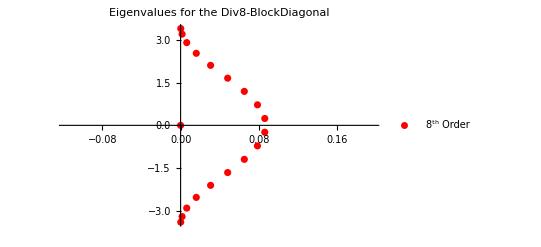

```mathematica
cplot8=ComplexListPlot[vals8,PlotRange->Automatic,PlotLabel->"Eigenvalues for the Div8-BlockDiagonal",AspectRatio->1/GoldenRatio,PlotStyle->Red, PlotLegends->{"8^th Order"}]
```

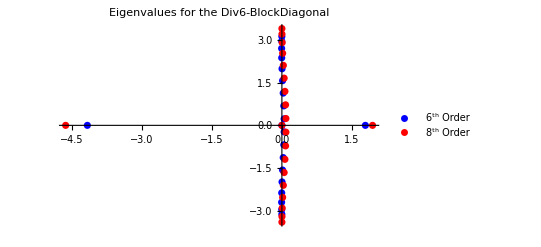

```mathematica
Show[cplot6, cplot8,PlotRange->Automatic,AspectRatio->1/GoldenRatio]
```

```mathematica
(lvals8=Eigenvalues[DDIV8.grad8])//MatrixForm//N
(lvals6=Eigenvalues[DDIV6.grad6])//MatrixForm//N
k=Table[i π/R,{i,1,n}];
λ=-k^2;
```

(-33.8553
-12.7042
-11.9775
-11.5363
-10.9493
-10.2328
-9.32963
-8.45456
-7.43709
-6.48722
-5.5168
-4.64233
-3.73753
-3.00535
-2.3131
-1.67835
-1.14832
-0.759836
-0.416928
-0.147239
0.)

(-20.5698
-10.0069
-9.82147
-9.20864
-8.82265
-7.85958+0.278313 ⅈ
-7.85958-0.278313 ⅈ
-7.40795
-6.52645
-5.7535
-4.86812
-4.1267
-3.36498
-2.66762
-2.0586
-1.5299
-1.02916
-0.663788
-0.383061
-0.140308
0.)

```mathematica
plot0 = Plot[λ,{x,.2,1},PlotStyle->Red,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot8=Plot[lvals8,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot6=Plot[lvals6,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

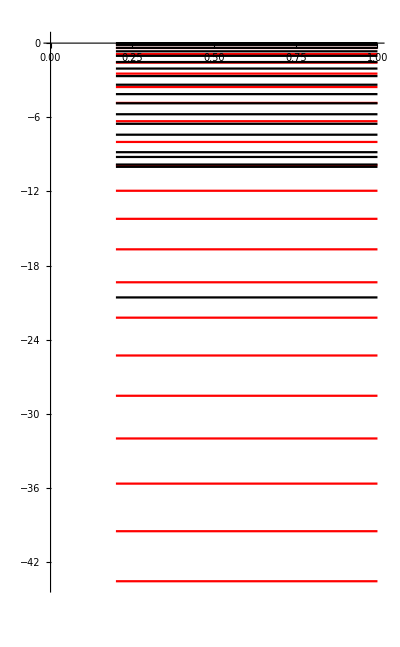

```mathematica
Show[plot0,plot6]
```

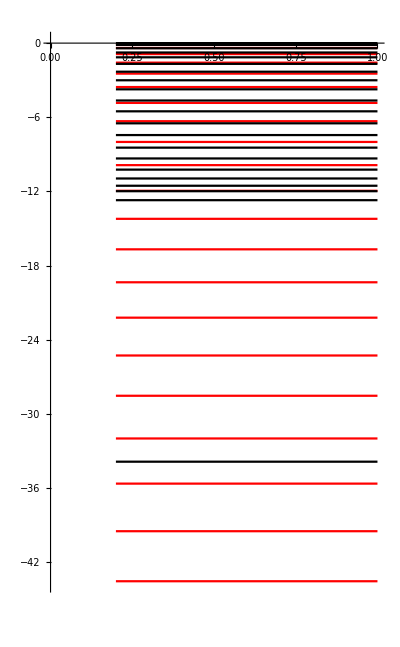

```mathematica
Show[plot0, plot8]
```